```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 1129 Kb

{Utilities`CleanSlate`,Parallel`Debug`Perfmon`,Parallel`Debug`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,System`,Global`}

```mathematica
(* See Howard Georgi *)
```

```mathematica
Clear[q]
q = { s1[t] , s2[t] , s3[t] , s4[t] }
```

{s1[t],s2[t],s3[t],s4[t]}

```mathematica
D[q, t]
```

{s1'[t],s2'[t],s3'[t],s4'[t]}

```mathematica
D[q, t] . D[q, t]
```

s1'[t]^2+s2'[t]^2+s3'[t]^2+s4'[t]^2

```mathematica
Clear[T]
T = 1/2 m ( D[q, t] . D[q, t] )
```

1/2 m (s1'[t]^2+s2'[t]^2+s3'[t]^2+s4'[t]^2)

```mathematica
Sum[ ( q[[i+1]] - q[[i]] )^2 , {  i , 1, 3 } ]
```

(-s1[t]+s2[t])^2+(-s2[t]+s3[t])^2+(-s3[t]+s4[t])^2

```mathematica
Clear[j]
j= 
Table[ Mod[i,4]+1 , { i , 0, 4 } ]
```

{1,2,3,4,1}

```mathematica
Sum[ ( q[[ j[[i+1]] ]] - q[[ j[[i]] ]] )^2 , { i, 1, 4 } ]
```

(-s1[t]+s2[t])^2+(-s2[t]+s3[t])^2+(s1[t]-s4[t])^2+(-s3[t]+s4[t])^2

```mathematica
1/4 Sum[ ( q[[ j[[i+1]] ]] - q[[ j[[i]] ]] )^2 , { i, 1, 4 } ]  // Expand // Simplify // TraditionalForm
```

1/2 (-s1(t) (s2(t)+s4(t))+(s1(t))^2-s2(t) s3(t)+(s2(t))^2-s3(t) s4(t)+(s3(t))^2+(s4(t))^2)

```mathematica
(* Look at s1[t] term carefully, it factored *)
```

```mathematica
Clear[V]
V = 
k (1/4)Sum[ ( q[[ j[[i+1]] ]] - q[[ j[[i]] ]] )^2 , { i, 1, 4 } ]  // Expand // Simplify
```

1/2 k (s1[t]^2+s2[t]^2-s2[t] s3[t]+s3[t]^2-s3[t] s4[t]+s4[t]^2-s1[t] (s2[t]+s4[t]))

```mathematica
Clear[ℒ]
ℒ = T - V ; 
ℒ // pdConv
```

1/2 m (((∂s1(t))/(∂t))^2+((∂s2(t))/(∂t))^2+((∂s3(t))/(∂t))^2+((∂s4(t))/(∂t))^2)-1/2 k (-s1(t) (s2(t)+s4(t))+(s1(t))^2-s2(t) s3(t)+(s2(t))^2-s3(t) s4(t)+(s3(t))^2+(s4(t))^2)

```mathematica
D[ ℒ , D[q[[1]], t] ] - D[ ℒ , q[[1]] ] 
D[ ℒ , D[q[[2]], t] ] - D[ ℒ , q[[2]] ] 
D[ ℒ , D[q[[3]], t] ] - D[ ℒ , q[[3]] ] 
D[ ℒ , D[q[[4]], t] ] - D[ ℒ , q[[4]] ]
```

1/2 k (2 s1[t]-s2[t]-s4[t])+m s1'[t]

1/2 k (-s1[t]+2 s2[t]-s3[t])+m s2'[t]

1/2 k (-s2[t]+2 s3[t]-s4[t])+m s3'[t]

1/2 k (-s1[t]-s3[t]+2 s4[t])+m s4'[t]

```mathematica
Table[ 
D[ ℒ , D[q[[i]], t] ] - D[ ℒ , q[[i]] ]== 0 ,
{ i, 1, 4 } ]  // Expand // TableForm
```

k s1[t]-1/2 k s2[t]-1/2 k s4[t]+m s1'[t]==0
-1/2 k s1[t]+k s2[t]-1/2 k s3[t]+m s2'[t]==0
-1/2 k s2[t]+k s3[t]-1/2 k s4[t]+m s3'[t]==0
-1/2 k s1[t]-1/2 k s3[t]+k s4[t]+m s4'[t]==0

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // Expand // TableForm
```

-k s1[t]+1/2 k s2[t]+1/2 k s4[t]-m s1''[t]==0
1/2 k s1[t]-k s2[t]+1/2 k s3[t]-m s2''[t]==0
1/2 k s2[t]-k s3[t]+1/2 k s4[t]-m s3''[t]==0
1/2 k s1[t]+1/2 k s3[t]-k s4[t]-m s4''[t]==0

```mathematica
Clear[parameters]
parameters = { 
m-> 10 , 
k -> 20 
} ;
parameters // TableForm
```

m→10
k→20

```mathematica
eqs /. parameters // Expand // TableForm
```

-20 s1[t]+10 s2[t]+10 s4[t]-10 s1''[t]==0
10 s1[t]-20 s2[t]+10 s3[t]-10 s2''[t]==0
10 s2[t]-20 s3[t]+10 s4[t]-10 s3''[t]==0
10 s1[t]+10 s3[t]-20 s4[t]-10 s4''[t]==0

```mathematica
Clear[ics]
ics = { 
s1[0] == π/2 - 0.2 ,
s1'[0] == 0 ,
s2[0] == π/2 ,
s2'[0] == 0 ,
s3[0] == π/2 ,
s3'[0] == 0 ,
s4[0] == π/2 ,
s4'[0] == 0 
} ;
ics // TableForm
```

s1[0]==1.3708
s1'[0]==0
s2[0]==π/2
s2'[0]==0
s3[0]==π/2
s3'[0]==0
s4[0]==π/2
s4'[0]==0

```mathematica
Clear[solution]
solution[t_] = 
First[ NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0, 100} ]  ]
```

{s1[t]→InterpolatingFunction[…][t],s2[t]→InterpolatingFunction[…][t],s3[t]→InterpolatingFunction[…][t],s4[t]→InterpolatingFunction[…][t]}

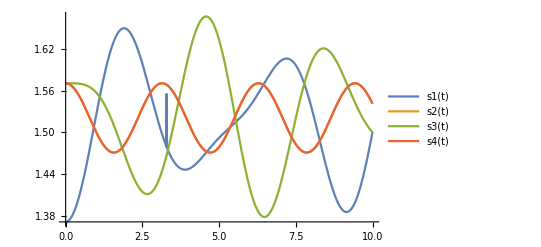

```mathematica
Plot[ Evaluate[  q /. solution [t] ] , { t, 0, 10 } , PlotLegends-> q  ]
```

```mathematica
solution[t]
solution[t][[1]]
solution[t][[1,2]]
```

{s1[t]→InterpolatingFunction[…][t],s2[t]→InterpolatingFunction[…][t],s3[t]→InterpolatingFunction[…][t],s4[t]→InterpolatingFunction[…][t]}

s1[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 0.1 , 20   } ]
```

```mathematica
solution[t]
solution[t][[2]]
solution[t][[2,2]]
```

{s1[t]→InterpolatingFunction[…][t],s2[t]→InterpolatingFunction[…][t],s3[t]→InterpolatingFunction[…][t],s4[t]→InterpolatingFunction[…][t]}

s2[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, tmax } , AxesLabel-> { q[[2]] , D[q[[2]], t] } ]  ,
{ tmax , 0.11 , 20 } ]
```

```mathematica
solution[t]
solution[t][[3]]
solution[t][[3,2]]
```

{s1[t]→InterpolatingFunction[…][t],s2[t]→InterpolatingFunction[…][t],s3[t]→InterpolatingFunction[…][t],s4[t]→InterpolatingFunction[…][t]}

s3[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[3,2]] , solution'[t][[3,2]] } , { t , 0, tmax } , AxesLabel-> { q[[3]] , D[q[[3]], t] } ]  ,
{ tmax , 0.1 , 50 } ]
```

```mathematica
solution[t]
solution[t][[4]]
solution[t][[4,2]]
```

{s1[t]→InterpolatingFunction[…][t],s2[t]→InterpolatingFunction[…][t],s3[t]→InterpolatingFunction[…][t],s4[t]→InterpolatingFunction[…][t]}

s4[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[4,2]] , solution'[t][[4,2]] } , { t , 0, tmax } , AxesLabel-> { q[[4]] , D[q[[4]], t] } ]  ,
{ tmax , 0.1 , 20 } ]
```